# Coupled catastrophes: sudden shifts cascade and hop among interdependent systems

## Charles D. Brummitt, George Barnett, Raissa M. D’Souza

## About this document

This document provides the code used to make the figures for the theoretical model in the open access paper

Brummitt, C. D., Barnett, G., & D’Souza, R. M. (2015). Coupled catastrophes: sudden shifts cascade and hop among interdependent systems. Journal of the Royal Society Interface, 12(112), 20150712. http://doi.org/10.1098/rsif.2015.0712

### Contact information

Charlie Brummitt: c.brummitt@columbia.edu

## Locations of saddle-node bifurcations

### master subsystem

The saddle-node bifurcations for the master system are the (x,a) at which ∂_t x(t)==0 and ∂_(x,t) x(t)==0:

```mathematica
Solve[{-x^3+x+a==0,D[-x^3+x+a,x]==0},{x,a}]
```

{{x→-1/(√3),a→2/(3 √3)},{x→1/(√3),a→-2/(3 √3)}}

### slave subsystem

Similarly, the saddle-node bifurcations for the slave system occur at

```mathematica
Simplify@Module[{slaveFlow=y^3-y+b+coupling[x,ϵ]},Solve[{slaveFlow==0,D[slaveFlow,y]==0},{y,b}]]
```

{{y→-1/(√3),b→-2/(3 √3)-coupling[x,ϵ]},{y→1/(√3),b→2/(3 √3)-coupling[x,ϵ]}}

```mathematica
Module[{slaveFlow=y^3-y+b+ϵ x},Solve[{slaveFlow==0,D[slaveFlow,y]==0},{y,b}]]
```

{{y→-1/(√3),b→1/9 (-2 √3-9 x ϵ)},{y→1/(√3),b→1/9 (2 √3-9 x ϵ)}}

### code to compute the saddle-node bifurcations for the slave system

Here, coupling[x,ϵ] is a coupling function.

```mathematica
computeSNBsForB[a_,ϵ_,coupling_]:={-2/(3 √3)-coupling[x,ϵ],2/(3 √3)-coupling[x,ϵ]}/.(Sort[Select[Solve[(-x^3+x+a)==0,x],Chop[Im[x/.#]]==0.&],(x/.#1)<(x/.#2)&])
```

## Figure 1: Single system in isolation

### figure for the paper (Fig. 1)

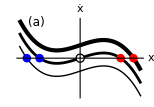
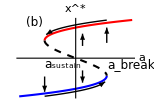

```mathematica
Module[{masterFlow,slaveFlow,slaveSlaveFlow,coupling,a0=-1,x0=-.6,y0=-.6,z0=-.6,yFixedPoints,zFixedPoints,sep="  "(*"\t"*),masterSNBs,aValuesToPlot,fs=12,imgSize=(*8.7 72/2.54*).65 8.4/2.54*72,aspectRatio=(*1/GoldenRatio*).7,upperColor=Red,lowerColor=Blue,pointSize=.04,font="Times"},
Block[{a,b,x},
masterFlow=-x^3+x+a;
x0=First[Sort[Select[x/.Solve[(masterFlow/.a->a0)==0,x],Im[#]==0&],Abs[#1-x0]<Abs[#2-x0]&]];
masterSNBs=Evaluate[a/.Solve[{masterFlow==0,D[masterFlow,x]==0},{x,a}]];
aValuesToPlot=Sort[{a->0}~Join~((a->#)&/@(2.5 masterSNBs)),(a/.#1)<(a/.#2)&];
Row[{Plot[Evaluate[Table[masterFlow/.av,{av,aValuesToPlot}]](*{masterFlow/.a->0,masterFlow/.a->masterSNBs⟦1⟧ 1.5}*),{x,-1.5,1.5},ImageSize->imgSize,AspectRatio->aspectRatio,AxesLabel->(Style[#,{FontSize->fs,FontFamily->font}]&/@{x,ẋ}),PlotStyle->{{Black,AbsoluteThickness[1]},{Black,AbsoluteThickness[2]},{Black,AbsoluteThickness[3]}},Ticks->None,
PlotRangeClipping->False,Epilog->Table[(If[Im[#]==0.,Which[#≤-1/(√3),{lowerColor,PointSize[pointSize],Point[{#,0}]},#>1/(√3),{upperColor,PointSize[pointSize],Point[{#,0}]},True,{{Black,PointSize[pointSize 1.1],Point[{#,0}]},{White,PointSize[pointSize*.8],Point[{#,0}]}}],{}]&/@Sort[x/.Solve[(masterFlow/.av)==0,x]]),{av,aValuesToPlot}]~Join~{Inset[Style["(a)",{FontSize->fs,FontFamily->font}],Scaled[{0.15,.95}]]}
,PlotLegends->Placed[LineLegend[Style[#,{FontSize->fs,FontFamily->font}]&/@{"a < a_sustain","a = 0","a > a_break"},
LegendMarkerSize->11,LegendLayout->Function[pairs,TableForm[pairs,TableAlignments->Left,TableSpacing->{0,.4}]]
],Scaled[{.83,.95}]]],
Plot[Evaluate[x/.Solve[masterFlow==0,x]],{a,-.7,.7},ImageSize->imgSize,AspectRatio->aspectRatio,AxesLabel->(Style[#,{FontSize->fs,FontFamily->font}]&/@{a,SuperStar[x]}),PlotStyle->{{lowerColor,AbsoluteThickness[1.5]},{upperColor,AbsoluteThickness[1.5]},{Black,Dashed,AbsoluteThickness[1.5]}},PlotRange->Full(*{-1.5,1.5}*),Ticks->{Transpose[{Sort@masterSNBs,{"",""}}],None},
Epilog->{
Inset[Style["(b)",{FontSize->fs,FontFamily->font}],Scaled[{0.15,.95}]],
Inset[Style["a_sustain",{FontSize->fs,FontFamily->font}],{Min@Sort@masterSNBs,0},{-.5,.8}],Inset[Style["a_break",{FontSize->fs,FontFamily->font}],{Max@Sort@masterSNBs,0},{-.5,.8}],

(*short arrows to the critical manifold (the fast flow)*)
{Arrowheads[
{{Small,0},{Small,1/2},{Small,1}}],Arrow[{{First@masterSNBs,.5},{First@masterSNBs,1}}],Arrow[{{First@masterSNBs-.3,.5-.1},{First@masterSNBs-.3,1-.1-.1}}],Arrow[{{First@masterSNBs-.3,-.4},{First@masterSNBs-.3,-.8}}],Arrow[{{Last@masterSNBs(*-.4*),-.6},{Last@masterSNBs(*-.4*),-1.1}}]}

(*long arrows along the critical manifold (the slow flow)*)
,{Arrowheads[
{{Small,1}}],Arrow[Table[{a,.09+Max@Evaluate[x/.Solve[masterFlow==0,x]]},{a,First@masterSNBs(*-.05*),Last@masterSNBs(*+.05*),-.05}]
],Arrow[Table[{a,-.09+Min@Evaluate[x/.Solve[masterFlow==0,x]]},{a,Last@masterSNBs,First@masterSNBs(*-.05*),.05}]
]}
}
]},sep]

]]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"figure1.pdf"}],%];
```

### figure for talks

#### with legend and tick labels

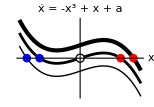
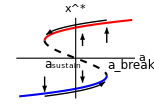

```mathematica
Module[{masterFlow,slaveFlow,slaveSlaveFlow,coupling,a0=-1,x0=-.6,y0=-.6,z0=-.6,yFixedPoints,zFixedPoints,sep="  "(*"\t"*),masterSNBs,aValuesToPlot,fs=12,imgSize=(*8.7 72/2.54*).65 8.4/2.54*72,aspectRatio=(*1/GoldenRatio*).7,upperColor=Red,lowerColor=Blue,pointSize=.04,font="Times"},
Block[{a,b,x},
masterFlow=-x^3+x+a;
x0=First[Sort[Select[x/.Solve[(masterFlow/.a->a0)==0,x],Im[#]==0&],Abs[#1-x0]<Abs[#2-x0]&]];
masterSNBs=Evaluate[a/.Solve[{masterFlow==0,D[masterFlow,x]==0},{x,a}]];
aValuesToPlot=Sort[{a->0}~Join~((a->#)&/@(2.5 masterSNBs)),(a/.#1)<(a/.#2)&];
{Plot[Evaluate[Table[masterFlow/.av,{av,aValuesToPlot}]](*{masterFlow/.a->0,masterFlow/.a->masterSNBs⟦1⟧ 1.5}*),{x,-1.5,1.5},ImageSize->imgSize,AspectRatio->aspectRatio,AxesLabel->(Style[#,{FontSize->fs,FontFamily->font}]&/@{x,"ẋ = -x^3 + x + a"}),PlotStyle->{{Black,AbsoluteThickness[1]},{Black,AbsoluteThickness[2]},{Black,AbsoluteThickness[3]}},Ticks->None,
PlotRangeClipping->False,Epilog->Table[(If[Im[#]==0.,Which[#≤-1/(√3),{lowerColor,PointSize[pointSize],Point[{#,0}]},#>1/(√3),{upperColor,PointSize[pointSize],Point[{#,0}]},True,{{Black,PointSize[pointSize 1.1],Point[{#,0}]},{White,PointSize[pointSize*.8],Point[{#,0}]}}],{}]&/@Sort[x/.Solve[(masterFlow/.av)==0,x]]),{av,aValuesToPlot}]
,PlotLegends->Placed[LineLegend[(*TableForm[(Style[#,FontSize->fs]&/@{"a < a_sustain","a = 0","a > a_break"})]*)Style[#,{FontSize->fs-2,FontFamily->font}]&/@{"a < a_sustain","a = 0","a > a_break"},
LegendMarkerSize->8,LegendLayout->Function[pairs,TableForm[pairs,TableAlignments->Left,TableSpacing->{0,0.3}]]
],Scaled[{.83,.9}]]],
Plot[Evaluate[x/.Solve[masterFlow==0,x]],{a,-.7,.7},ImageSize->imgSize,AspectRatio->aspectRatio,AxesLabel->(Style[#,{FontSize->fs,FontFamily->font}]&/@{a,SuperStar[x]}),PlotStyle->{{lowerColor,AbsoluteThickness[1.5]},{upperColor,AbsoluteThickness[1.5]},{Black,Dashed,AbsoluteThickness[1.5]}},PlotRange->Full(*{-1.5,1.5}*),Ticks->{Transpose[{Sort@masterSNBs,{"",""}}],None},
Epilog->{

Inset[Style["a_sustain",{FontSize->fs,FontFamily->font}],{Min@Sort@masterSNBs,0},{-.5,.8}],Inset[Style["a_break",{FontSize->fs,FontFamily->font}],{Max@Sort@masterSNBs,0},{-.5,.8}],
(*short arrows to the critical manifold (the fast flow)*)
{Arrowheads[
{{Small,0},{Small,1/2},{Small,1}}],Arrow[{{First@masterSNBs,.5},{First@masterSNBs,1}}],Arrow[{{First@masterSNBs-.3,.5-.1},{First@masterSNBs-.3,1-.1-.1}}],Arrow[{{First@masterSNBs-.3,-.4},{First@masterSNBs-.3,-.8}}],Arrow[{{Last@masterSNBs(*-.4*),-.6},{Last@masterSNBs(*-.4*),-1.1}}]}

(*long arrows along the critical manifold (the slow flow)*)
,{Arrowheads[
{{Small,1}}],Arrow[Table[{a,.09+Max@Evaluate[x/.Solve[masterFlow==0,x]]},{a,First@masterSNBs(*-.05*),Last@masterSNBs(*+.05*),-.05}]
],Arrow[Table[{a,-.09+Min@Evaluate[x/.Solve[masterFlow==0,x]]},{a,Last@masterSNBs,First@masterSNBs(*-.05*),.05}]
]}
}
]}

]]
```

#### without legend nor tick labels

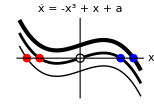
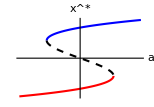

```mathematica
Module[{masterFlow,slaveFlow,slaveSlaveFlow,coupling,a0=-1,x0=-.6,y0=-.6,z0=-.6,yFixedPoints,zFixedPoints,sep="  "(*"\t"*),masterSNBs,aValuesToPlot,fs=12,imgSize=(*8.7 72/2.54*).65 8.4/2.54*72,aspectRatio=(*1/GoldenRatio*).7,upperColor=Blue,lowerColor=Red,pointSize=.04,font="Times"},
Block[{a,b,x},
masterFlow=-x^3+x+a;
x0=First[Sort[Select[x/.Solve[(masterFlow/.a->a0)==0,x],Im[#]==0&],Abs[#1-x0]<Abs[#2-x0]&]];
masterSNBs=Evaluate[a/.Solve[{masterFlow==0,D[masterFlow,x]==0},{x,a}]];
aValuesToPlot=Sort[{a->0}~Join~((a->#)&/@(2.5 masterSNBs)),(a/.#1)<(a/.#2)&];
{Plot[Evaluate[Table[masterFlow/.av,{av,aValuesToPlot}]](*{masterFlow/.a->0,masterFlow/.a->masterSNBs⟦1⟧ 1.5}*),{x,-1.5,1.5},ImageSize->imgSize,AspectRatio->aspectRatio,AxesLabel->(Style[#,{FontSize->fs,FontFamily->font}]&/@{x,"ẋ = -x^3 + x + a"}),PlotStyle->{{Black,AbsoluteThickness[1]},{Black,AbsoluteThickness[2]},{Black,AbsoluteThickness[3]}},Ticks->None,
PlotRangeClipping->False,Epilog->(*({Which[#≤-1/(√3),lowerColor,#>1/(√3),upperColor,True,White],PointSize[pointSize],Point[{#,0}]}&/@Sort[x/.Solve[(-x^3+x+a/.a->0)==0,x]])*)(*(Which[#≤-1/(√3),{lowerColor,PointSize[pointSize],Point[{#,0}]},#>1/(√3),{upperColor,PointSize[pointSize],Point[{#,0}]},True,{{Black,PointSize[pointSize 1.1],Point[{#,0}]},{White,PointSize[pointSize*.8],Point[{#,0}]}}]&/@Sort[x/.Solve[(masterFlow/.a->0)==0,x]])*)Table[(If[Im[#]==0.,Which[#≤-1/(√3),{lowerColor,PointSize[pointSize],Point[{#,0}]},#>1/(√3),{upperColor,PointSize[pointSize],Point[{#,0}]},True,{{Black,PointSize[pointSize 1.1],Point[{#,0}]},{White,PointSize[pointSize*.8],Point[{#,0}]}}],{}]&/@Sort[x/.Solve[(masterFlow/.av)==0,x]]),{av,aValuesToPlot}](*~Join~{Inset[Style["(a)",{FontSize->fs,FontFamily->"Times"}],Scaled[{0.15,.95}]](*,Inset[Style[a<Subscript[a, sustain],FontSize->fs],Scaled[{0.8,.1}]],Inset[Style[a>Subscript[a, sustain],FontSize->fs],Scaled[{0.8,.8}]]*)}*)
(*,PlotLegends->Placed[LineLegend[(*TableForm[(Style[#,FontSize->fs]&/@{"a < a_sustain","a = 0","a > a_break"})]*)Style[#,{FontSize->fs-2,FontFamily->font}]&/@{"a < a_sustain","a = 0","a > a_break"},
LegendMarkerSize->8,LegendLayout->Function[pairs,TableForm[pairs,(*TableHeadings->{(Style[#,FontSize->fs]&/@{"a < a_sustain","a = 0","a > a_break"}),None},*)TableAlignments->Left,TableSpacing->{0,0.3}]]
],Scaled[{.83,.9}]]*)],
Plot[Evaluate[x/.Solve[masterFlow==0,x]],{a,-.7,.7},ImageSize->imgSize,AspectRatio->aspectRatio,AxesLabel->(Style[#,{FontSize->fs,FontFamily->font}]&/@{a,SuperStar[x]}),PlotStyle->{{lowerColor,AbsoluteThickness[1.5]},{upperColor,AbsoluteThickness[1.5]},{Black,Dashed,AbsoluteThickness[1.5]}},(*Epilog->{PointSize[Large],If[x0≤-1/(√3),lowerColor,upperColor],Point[{a0,x0}]},*)PlotRange->Full(*{-1.5,1.5}*),Ticks->{(*Transpose[{Sort@masterSNBs,(Style[#,FontSize->fs]&/@{"a_sustain","     a_break"})}]*)Transpose[{Sort@masterSNBs,{"",""}}],None}(*,
Epilog->{
(*Inset[Style["(b)",{FontSize->fs,FontFamily->"Times"}],Scaled[{0.15,.95}]],*)
Inset[Style["a_sustain",{FontSize->fs,FontFamily->font}],{Min@Sort@masterSNBs,0},{-.5,.8}],Inset[Style["a_break",{FontSize->fs,FontFamily->font}],{Max@Sort@masterSNBs,0},{-.5,.8}],
(*short arrows to the critical manifold (the fast flow)*)
{Arrowheads[
{{Small,0},{Small,1/2},{Small,1}}],Arrow[{{First@masterSNBs,.5},{First@masterSNBs,1}}],Arrow[{{First@masterSNBs-.3,.5-.1},{First@masterSNBs-.3,1-.1-.1}}],Arrow[{{First@masterSNBs-.3,-.4},{First@masterSNBs-.3,-.8}}],Arrow[{{Last@masterSNBs(*-.4*),-.6},{Last@masterSNBs(*-.4*),-1.1}}]}

(*long arrows along the critical manifold (the slow flow)*)
,{Arrowheads[
{(*{Small,1/2},*){Small,1}}],Arrow[Table[{a,.09+Max@Evaluate[x/.Solve[masterFlow==0,x]]},{a,First@masterSNBs(*-.05*),Last@masterSNBs(*+.05*),-.05}]
],Arrow[Table[{a,-.09+Min@Evaluate[x/.Solve[masterFlow==0,x]]},{a,Last@masterSNBs,First@masterSNBs(*-.05*),.05}]
]}
}*)
]}

]]
```

## Figure 2: Master–slave with linear coupling

### Figure 2

Here, the slave subsystem’s saddle-node bifurcations are determined by the equilibria x^* of the master system. 

We choose a_0:=0.7 to be larger than its “break point” saddle-node bifurcation a_break, so that the master system is facilitating the slave system (encouraging it to pass its break point b_break).

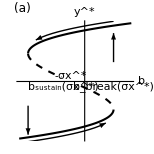
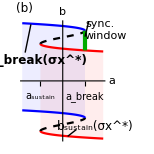
-Graphics- | -Graphics-

```mathematica
Module[{masterFlow,slaveFlow,slaveSlaveFlow,coupling,a0=.7,x0=1.6,y0=-.6,z0=-.6,yFixedPoints,zFixedPoints,sep=(*"\t"*)"",masterSNBs,slaveSNBs,ϵ0=.1,b0=-1,c0=-1,fs=12,fsTicks=11,font="Times",imgSize= (*8.7 72/2.54*).65 8.4/2.54*72,aspectRatio=(*1/GoldenRatio*)1,upperColor=Red,lowerColor=Blue,pointSize=.035,syncWindow},
Block[{a,b,x},
masterFlow=-x^3+x+a;
coupling=#1 #2&;
slaveFlow=-y^3+y+b+coupling[x,ϵ];
slaveSlaveFlow=-z^3+z+c+coupling[y,ϵ];

x0=First[Sort[Select[x/.Solve[(masterFlow/.a->a0)==0,x],Im[#]==0&],Abs[#1-x0]<Abs[#2-x0]&]];(*Print[N@x0];*)
y0=First[Sort[Select[y/.Solve[(slaveFlow/.{b->b0,x->x0,ϵ->ϵ0})==0,y],Im[#]==0.&],Abs[#1-y0]<Abs[#2-y0]&]];
masterSNBs=Evaluate[a/.Solve[{masterFlow==0,D[masterFlow,x]==0},{x,a}]];(*Print[N@masterSNBs];*)
slaveSNBs=Evaluate[b/.NSolve[({slaveFlow==0,D[slaveFlow,y]==0}/.{x->x0,ϵ->ϵ0}),{y,b}]];

yFixedPoints=y/.Quiet[Solve[(slaveFlow/.{x->x0,ϵ->ϵ0})==0,y]];
zFixedPoints=z/.Quiet[Solve[(slaveSlaveFlow/.{y->y0,ϵ->ϵ0})==0,z]];
syncWindow={Last@First@Chop[computeSNBsForB[a,ϵ0,coupling]/.Solve[masterFlow==0,x]/.a->First[masterSNBs]],Part[#,2,2]&@Chop[computeSNBsForB[a,ϵ0,coupling]/.Solve[masterFlow==0,x]/.a->First[masterSNBs]]};

Grid[{{Plot[yFixedPoints,{b,-.59,.42},ImageSize->imgSize,AspectRatio->aspectRatio,AxesLabel->(Style[#,{FontSize->fsTicks,FontFamily->font}]&/@{b,SuperStar[y]}),PlotStyle->{{Black,AbsoluteThickness[1.5]},{Black,AbsoluteThickness[1.5]},{Black,Dashed,AbsoluteThickness[1.5]}},PlotRange->Full,Ticks->{Transpose[{Sort@slaveSNBs,(Style[#,{FontSize->fsTicks,FontFamily->font}]&/@{"",""}),{.05,.05}}]~Join~{{-ϵ0 x0,"",.05}},None},Epilog->{Inset[Style["(a)",{FontFamily->font,FontSize->fs}],Scaled[{.05,1.1}]],Inset[Style["-σx^*",{FontFamily->font,FontSize->fsTicks}],{-ϵ0 x0,0},{.0,-1.5}],Inset[Style["b_sustain(σx^*) ",{FontFamily->font,FontSize->fsTicks}],{Min[Sort@slaveSNBs],0},{-.55,1.5}],Inset[Style["b_break(σx^*)",{FontFamily->font,FontSize->fsTicks}],{Max[Sort@slaveSNBs],0},{-0.2,1.5}],

(*short arrows to the critical manifold (the fast flow)*)
{Arrowheads[
{{Small,0},{Small,1/2},{Small,1}}],Arrow[{{First@slaveSNBs,.4},{First@slaveSNBs,1}}],Arrow[{{Last@slaveSNBs,-.5},{Last@slaveSNBs,-1.1}}]}

(*long arrows along the critical manifold (the slow flow)*)
,{Arrowheads[
{{Small,1}}],Arrow[Table[{b,-.09+Min@Re@Chop@yFixedPoints},{b,Min@slaveSNBs,Max@slaveSNBs-.05,.05}]
],Arrow[Table[{b,.09+Max@Re@Chop@yFixedPoints},{b,Max@slaveSNBs,Min@slaveSNBs+.05,-.05}]
]}},PlotRangeClipping->False],

Show[Plot[Evaluate@Flatten[computeSNBsForB[a,ϵ0,coupling]/.Solve[masterFlow==0,x]],{a,-.7,.7},AxesLabel->(Style[#,{FontSize->fs,FontFamily->font,Italic}]&/@{"a","b"(*Row[{"b_sustain(x^*),",Style[" b_break(x^*)",Bold]}]*)}),PlotStyle->{{Blue},{Blue,Thick},{Red},{Red,Thick},{Black,Dashed},{Black,Dashed,Thick}},Filling->{1->{{2},Directive[Lighter@Blue,Opacity[.1]]},3->{{4},Directive[Lighter@Red,Opacity[.1]]}},ImageSize->imgSize,PlotRange->Full,PlotRangeClipping->False,Ticks->{{{-2/(3 √3),Style["a_sustain",{FontSize->fsTicks,FontFamily->font}],.05},{2/(3 √3),Style["a_break",{FontSize->fsTicks,FontFamily->font}],.05}},None},Epilog->{{PointSize[Large],If[x0≤-1/(√3),Blue,Red],Point[{a0,b0}]}}~Join~{Inset[Style["b_break(σx^*)",{FontSize->fs,FontFamily->font,Bold}],Scaled[{.2,.67}]],
BezierCurve[{{-.65,.25},{-.55,.5}}],
Inset[Style["b_sustain(σx^*)",{FontSize->fs,FontFamily->font}],Scaled[{.88,.12}]],Inset[Style["(b)",{FontFamily->font,FontSize->fs}],Scaled[{.05,1.1}]]
,{Darker@Green,AbsoluteThickness[3],Line[Transpose[{{First[masterSNBs],First[masterSNBs]},syncWindow}]]}
,Inset[Column[{Style["sync.",{FontSize->fs,FontFamily->font,Darker@Green}],Style["window",{FontSize->fs,FontFamily->font,Darker@Green}]},Left,.1],{First[masterSNBs],Mean@syncWindow},{-1.4,-1.6}]
,Line[{{First[masterSNBs],{.7,.3}.syncWindow},{First[masterSNBs]+.07,Mean@syncWindow+.18}}]

,Line[{{First[masterSNBs]-.3,-.49},{First[masterSNBs]-.15,-.43}}]
},PlotLegends->Placed[LineLegend[{Directive[lowerColor,Thick],Directive@@{Dashed,Black,Thick},Directive@@{upperColor,Thick}},{Style["lower ",{FontSize->fsTicks,FontFamily->"Times",lowerColor}],Style["middle ",{FontSize->fsTicks,FontFamily->"Times"}],Style["upper branch",{FontSize->fsTicks,FontFamily->"Times",upperColor}]},LegendLayout->(Row[{Style["x^* on its ",{FontSize->fsTicks,FontFamily->"Times"}]}~Join~(Row[#," "]&/@#),""]&),LegendMarkerSize->7],Bottom]],AspectRatio-> aspectRatio]
}},Spacings->{-.5,0}]

]]
```

### show paths through the “synchronizing window”

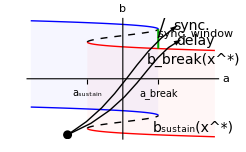

```mathematica
Module[{masterFlow,slaveFlow,slaveSlaveFlow,coupling,a0=-1,x0=-.6,y0=-.6,z0=-.6,yFixedPoints,zFixedPoints,sep="\t",masterSNBs,slaveSNBs,ϵ0=.1,b0=-1,c0=-1,fs=14,fsTicks=11,imgSize= 8.7 72/2.54,aspectRatio=1/GoldenRatio,upperColor=Red,lowerColor=Blue,pointSize=.035 .75,syncWindow,initialParameters={-.6,-.5}},
Block[{a,b,x},
masterFlow=-x^3+x+a;
coupling=#1 #2&;
slaveFlow=-y^3+y+b+coupling[x,ϵ];
slaveSlaveFlow=-z^3+z+c+coupling[y,ϵ];

x0=First[Sort[Select[x/.Solve[(masterFlow/.a->a0)==0,x],Im[#]==0&],Abs[#1-x0]<Abs[#2-x0]&]];
y0=First[Sort[Select[y/.Solve[(slaveFlow/.{b->b0,x->x0,ϵ->ϵ0})==0,y],Im[#]==0.&],Abs[#1-y0]<Abs[#2-y0]&]];
masterSNBs=Evaluate[a/.Solve[{masterFlow==0,D[masterFlow,x]==0},{x,a}]];
slaveSNBs=Evaluate[b/.NSolve[({slaveFlow==0,D[slaveFlow,y]==0}/.{x->x0,ϵ->ϵ0}),{y,b}]];

yFixedPoints=y/.Quiet[Solve[(slaveFlow/.{x->x0,ϵ->ϵ0})==0,y]];
zFixedPoints=z/.Quiet[Solve[(slaveSlaveFlow/.{y->y0,ϵ->ϵ0})==0,z]];

syncWindow={Last@First@Chop[computeSNBsForB[a,ϵ0,coupling]/.Solve[masterFlow==0,x]/.a->First[masterSNBs]],Part[#,2,2]&@Chop[computeSNBsForB[a,ϵ0,coupling]/.Solve[masterFlow==0,x]/.a->First[masterSNBs]]};

(*Print[masterSNBs];
Print[First@Chop[computeSNBsForB[a,ϵ0,coupling]/.Solve[masterFlow==0,x]/.a->First[masterSNBs]]];
Print[{Last@First@Chop[computeSNBsForB[a,ϵ0,coupling]/.Solve[masterFlow==0,x]/.a->First[masterSNBs]],Part[#,2,2]&@Chop[computeSNBsForB[a,ϵ0,coupling]/.Solve[masterFlow==0,x]/.a->First[masterSNBs]]}];*)
Labeled[Column[{

Row[{Show[Plot[Evaluate@Flatten[computeSNBsForB[a,ϵ0,coupling]/.Solve[masterFlow==0,x]],{a,-1,1},AxesLabel->(Style[#,{FontSize->fs,Italic}]&/@{"a","b"(*Row[{"b_sustain(x^*),",Style[" b_break(x^*)",Bold]}]*)}),PlotStyle->{{Blue},{Blue,Thick},{Red},{Red,Thick},{Black,Dashed},{Black,Dashed,Thick}},Filling->{{1->{{2},{Directive[Lighter@Blue,Opacity[.05]]}}},{3->{{4},Directive[Lighter@Red,Opacity[.05]]}}},ImageSize->imgSize,PlotRange->Full(*{{0,1},{0,.8}}*)(*{-.5,.5}*),Ticks->{{{-2/(3 √3),Style["a_sustain",FontSize->fs]},{2/(3 √3),Style["a_break",FontSize->fs]}},None},Epilog->{{PointSize[Large],If[x0≤-1/(√3),Blue,Red],Point[{a0,b0}]}}~Join~{Inset[Style["b_break(x^*)",FontSize->fs],Scaled[{.87,.66}]],Inset[Style["b_sustain(x^*)",FontSize->fs],Scaled[{.87,.1}]](*,Inset[Style["B",FontSize->fs],Scaled[{.05,.8}]]*),{Darker@Green,AbsoluteThickness[1.5],Line[Transpose[{{First[masterSNBs],First[masterSNBs]},syncWindow}]]},
Inset[Column[{Style["sync. window",{FontSize->fs,Darker@Green}](*,Style["window",{FontSize->fs,Darker@Green}]*)},Alignment->Right],{First[masterSNBs],Mean@syncWindow},{-.9,-4.2}(*{-.45,-5}*)],
Line[{{First[masterSNBs],{.7,.2}.syncWindow},{First[masterSNBs]+.09,Mean@syncWindow+.24}}],
{PointSize[pointSize],Point[initialParameters]},
(*Arrow@BezierCurve[{initialParameters,{initialParameters⟦1⟧,.6}}],*)
Arrow@BezierCurve[{initialParameters,{0,-.2},{.1,.2},{First[masterSNBs]+.2,{.3,.7}.syncWindow+.15}}],
Arrow@BezierCurve[{initialParameters,{0.15,-.25},{.25,.2},{First[masterSNBs]+.24,{.3,.7}.syncWindow+.025}}],
Inset[Style["sync.",FontSize->fs],Scaled[{.86,.94}]],Inset[Style["delay",FontSize->fs],Scaled[{.88,.812}]]
},PlotRangeClipping->False,ImagePadding->{{10,20},{0,25}}]]
},sep]

}]

,"",Top]

]]
```

## Figure SM-1: Length of the synchronizing window

### calculation

The critical points of the master equation are

```mathematica
Module[{masterFlow,slaveFlow,coupling,(*a0=-1,*)x0=.6,y0=.6,yFixedPoints,sep="\t"},
(*Block[{(*a,b,*)a,x,y,ϵ},*)
masterFlow=-x^3+x+a;
coupling=#1 #2&;
slaveFlow=-y^3+y+b+coupling[x,ϵ];

Solve[{masterFlow==0,D[masterFlow,x]==0},{x,a}]
]
```

{{x→-1/(√3),a→2/(3 √3)},{x→1/(√3),a→-2/(3 √3)}}

Next we solve for the upper-branch value of x to which the master system snaps to at a=2/(3 √3):

```mathematica
Module[{masterFlow,slaveFlow,coupling,(*a0=-1,*)x0=.6,y0=.6,yFixedPoints,sep="\t"},
(*Block[{(*a,b,*)a,x,y,ϵ},*)
masterFlow=-x^3+x+a;
coupling=#1 #2&;
slaveFlow=-y^3+y+b+coupling[x,ϵ];

(*Solve[{masterFlow==0,D[masterFlow,x]==0},{x,a}]*)
Solve[masterFlow==0/.a->2/(3 √3),x]
]
```

{{x→-1/(√3)},{x→-1/(√3)},{x→2/(√3)}}

Now we solve for the value of b such that, at x=2/(√3), the slave flow is at a critical point:

```mathematica
Module[{masterFlow,slaveFlow,coupling,(*a0=-1,*)x0=.6,y0=.6,yFixedPoints,sep="\t"},
(*Block[{(*a,b,*)a,x,y,ϵ},*)
masterFlow=-x^3+x+a;
coupling=#1 #2&;
slaveFlow=-y^3+y+b+coupling[x,ϵ];

FullSimplify@Solve[{(slaveFlow/.x->2/(√3))==0,D[slaveFlow/.x->2/(√3),y]==0},{y,b}]
]
```

{{y→-1/(√3),b→(2 (1-3 ϵ))/(3 √3)},{y→1/(√3),b→-(2 (1+3 ϵ))/(3 √3)}}

The larger of these two, (2 (1-3 ϵ))/(3 √3), is what we want.

Now solve for the value of b such that, at x=-1/(√3), the slave flow is at a critical point:

```mathematica
Module[{masterFlow,slaveFlow,coupling,(*a0=-1,*)x0=.6,y0=.6,yFixedPoints,sep="\t"},
(*Block[{(*a,b,*)a,x,y,ϵ},*)
masterFlow=-x^3+x+a;
coupling=#1 #2&;
slaveFlow=-y^3+y+b+coupling[x,ϵ];

FullSimplify@Solve[{(slaveFlow/.x->-1/(√3))==0,D[slaveFlow/.x->-1/(√3),y]==0},{y,b}]
(*First[Sort[Select[x/.Solve[(masterFlow/.a->a0)==0,x],Im[#]==0&],Abs[#1-x0]<Abs[#2-x0]&]]*)
]
```

{{y→-1/(√3),b→(2+3 ϵ)/(3 √3)},{y→1/(√3),b→(-2+3 ϵ)/(3 √3)}}

The larger of these two, (2+3 ϵ)/(3 √3), is what we want.

In conclusion, the endpoints of the synchronizing window are

```mathematica
{(2 (1-3 ϵ))/(3 √3),(2+3 ϵ)/(3 √3)}
```

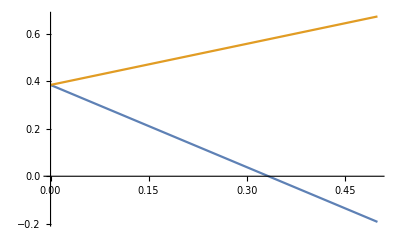

```mathematica
Plot[{(2 (1-3 ϵ))/(3 √3),(2+3 ϵ)/(3 √3)},{ϵ,0,.5}]
```

### create Figure SM-1

#### synchronizing window S versus coupling strenght σ

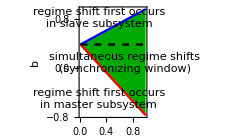

```mathematica
Module[{fs=10,fsTicks=10,font="Times",imgSize= (*8.7 72/2.54*).95 8.4/2.54*72,aspectRatio=1/GoldenRatio,upperColor=Red,lowerColor=Blue},Plot[{(2+3 ϵ)/(3 √3),(2 (1-3 ϵ))/(3 √3),2/(3 √3)},{ϵ,0,1},Frame->True,FrameLabel->({Column[{Style["coupling strength σ",{FontSize->fsTicks,FontFamily->Times}]}],Style["b",{FontSize->fsTicks,FontFamily->Times}]}),Axes->None,Filling->{1->{{2},(*LightGray*)Directive[Darker@Green(*,Opacity[.3]*)]}},Axes->{True,True},FrameStyle->Black,PlotStyle->{lowerColor,upperColor,{Black,Dashed}},ImageSize->imgSize,AspectRatio->aspectRatio,FrameTicksStyle->{{FontFamily->font,FontSize->fsTicks},{FontFamily->font,FontSize->fsTicks}},Epilog->{Inset[Column[{Style["simultaneous regime shifts",{FontFamily->font,White,FontSize->fsTicks}],Style["(synchronizing window)",{FontFamily->font,White,FontSize->fsTicks}]},Alignment->Right],{.68,.08}],Inset[Column[{Style["regime shift first occurs",{FontFamily->font,FontSize->fsTicks}],Style["in master subsystem",{FontFamily->font,FontSize->fsTicks}]},Alignment->Center,Spacings->{0,.2}],{.28,-.5}],Inset[Column[{Style["regime shift first occurs",{FontFamily->font,FontSize->fsTicks}],Style["in slave subsystem",{FontFamily->font,FontSize->fsTicks}]},Alignment->Center,Spacings->{0,.2}],{.29,.82}]}]]
```

#### Make figures showing how the b_break(σ x^*) S-shaped curves stretch as σ increases:

1.24915

{0.3849,-0.3849}

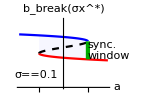
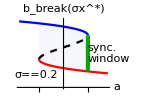
(a) | (b)
-Graphics- | -Graphics-

```mathematica
Module[{masterFlow,slaveFlow,slaveSlaveFlow,coupling,a0=.7,x0=1.6,y0=-.6,z0=-.6,yFixedPoints,zFixedPoints,sep=(*"\t"*)"",masterSNBs,slaveSNBs,ϵ0=.1,ϵ1=.2,b0=-1,c0=-1,fs=10,fsTicks=10,imgSize= (*8.7 72/2.54*)1/3 2* 8.4/2.54*72,aspectRatio=1/GoldenRatio,upperColor=Red,lowerColor=Blue,pointSize=.035,syncWindow,syncWindowLargerCoupling},
Block[{a,b,x},
masterFlow=-x^3+x+a;
coupling=#1 #2&;
slaveFlow=-y^3+y+b+coupling[x,ϵ];
slaveSlaveFlow=-z^3+z+c+coupling[y,ϵ];

x0=First[Sort[Select[x/.Solve[(masterFlow/.a->a0)==0,x],Im[#]==0&],Abs[#1-x0]<Abs[#2-x0]&]];Print[N@x0];
y0=First[Sort[Select[y/.Solve[(slaveFlow/.{b->b0,x->x0,ϵ->ϵ0})==0,y],Im[#]==0.&],Abs[#1-y0]<Abs[#2-y0]&]];
masterSNBs=Evaluate[a/.Solve[{masterFlow==0,D[masterFlow,x]==0},{x,a}]];Print[N@masterSNBs];
slaveSNBs=Evaluate[b/.NSolve[({slaveFlow==0,D[slaveFlow,y]==0}/.{x->x0,ϵ->ϵ0}),{y,b}]];

yFixedPoints=y/.Quiet[Solve[(slaveFlow/.{x->x0,ϵ->ϵ0})==0,y]];
zFixedPoints=z/.Quiet[Solve[(slaveSlaveFlow/.{y->y0,ϵ->ϵ0})==0,z]];
syncWindow={Last@First@Chop[computeSNBsForB[a,ϵ0,coupling]/.Solve[masterFlow==0,x]/.a->First[masterSNBs]],Part[#,2,2]&@Chop[computeSNBsForB[a,ϵ0,coupling]/.Solve[masterFlow==0,x]/.a->First[masterSNBs]]};

syncWindowLargerCoupling={Last@First@Chop[computeSNBsForB[a,ϵ1,coupling]/.Solve[masterFlow==0,x]/.a->First[masterSNBs]],Part[#,2,2]&@Chop[computeSNBsForB[a,ϵ1,coupling]/.Solve[masterFlow==0,x]/.a->First[masterSNBs]]};

stretchFigures=Labeled[Grid[{{Style["(a)",{FontSize->fs,FontFamily->"Times"}],Style["(b)",{FontSize->fs,FontFamily->"Times"}]},{Show[Plot[Evaluate@Flatten[computeSNBsForB[a,ϵ0,coupling]⟦2⟧/.Solve[masterFlow==0,x]],{a,-.7,.7},AxesLabel->(Style[#,{FontSize->fs,FontFamily->Times,Italic}]&/@{"a ","b_break(σx^*)"(*Row[{"b_sustain(x^*),",Style[" b_break(x^*)",Bold]}]*)}),PlotStyle->{(*{Blue},*){Blue,Thick},(*{Red},*){Red,Thick},(*{Black,Dashed},*){Black,Dashed,Thick}},Filling->{{1->{{2},{Directive[Lighter@Blue,Opacity[.05]]}}},{3->{{4},Directive[Lighter@Red,Opacity[.05]]}}},ImageSize->imgSize,PlotRange->{0,.65},PlotRangeClipping->False(*{-.5,.5}*),ImagePadding->{{Automatic,Automatic},{Automatic,25}},Ticks->{{{-2/(3 √3),Style["a_sustain",{FontSize->fsTicks,FontFamily->Times}],.05},{2/(3 √3),Style["a_break",{FontSize->fsTicks,FontFamily->Times}],.05}},None},AxesStyle->Black,Epilog->{Inset[Framed[σ == 0.1],Scaled[{.2,.2}]],{PointSize[Large],If[x0≤-1/(√3),Blue,Red],Point[{a0,b0}]}}~Join~{{Darker@Green,AbsoluteThickness[3],Line[Transpose[{{First[masterSNBs],First[masterSNBs]},syncWindow}]]}
,Inset[Column[{Style["sync.",{FontSize->fs,Darker@Green,FontFamily->"Times"}],Style["window",{FontSize->fs,Darker@Green,FontFamily->"Times"}]},Left,0],{First[masterSNBs],Mean@syncWindow},(*{-1.23,-.5}*){-1.3,-.1}]
}],AspectRatio->(*.8*) aspectRatio]
,
Show[Plot[Evaluate@Flatten[computeSNBsForB[a,ϵ1,coupling]⟦2⟧/.Solve[masterFlow==0,x]],{a,-.7,.7},AxesLabel->(Style[#,{FontSize->fs,FontFamily->Times,Italic}]&/@{"a","b_break(σx^*)"(*Row[{"b_sustain(x^*),",Style[" b_break(x^*)",Bold]}]*)}),PlotStyle->{(*{Blue},*){Blue,Thick},(*{Red},*){Red,Thick},(*{Black,Dashed},*){Black,Dashed,Thick}},ImagePadding->{{Automatic,Automatic},{Automatic,25}},Filling->{{1->{{2},{Directive[Lighter@Blue,Opacity[.05]]}}},{3->{{4},Directive[Lighter@Red,Opacity[.05]]}}},ImageSize->imgSize,PlotRange->{0,.65},PlotRangeClipping->False(*{-.5,.5}*),Ticks->{{{-2/(3 √3),Style["a_sustain",{FontSize->fsTicks,FontFamily->Times}],.05},{2/(3 √3),Style["a_break",{FontSize->fsTicks,FontFamily->Times}],.05}},None},AxesStyle->Black,Epilog->{Inset[Framed[σ == 0.2],Scaled[{.2,.2}]],{PointSize[Large],If[x0≤-1/(√3),Blue,Red],Point[{a0,b0}]}}~Join~{{Darker@Green,AbsoluteThickness[3],Line[Transpose[{{First[masterSNBs],First[masterSNBs]},syncWindowLargerCoupling}]]}
,Inset[Column[{Style["sync.",{FontSize->fs,Darker@Green,FontFamily->"Times"}],Style["window",{FontSize->fs,Darker@Green,FontFamily->"Times"}]},Left,0],{First[masterSNBs],Mean@syncWindowLargerCoupling},{-1.3,-.1}]
}],AspectRatio->(*.8*) aspectRatio]}

},Alignment->Left,Spacings->{0,-.5}],LineLegend[{Directive[lowerColor,Thick],Directive@@{Dashed,Black,Thick},Directive@@{upperColor,Thick}},(*{"x^* = x_upper(a)","x^* = x_lower(a)"}*)(*{"x^* on lower branch","x^* on middle branch","x^* on upper branch"}*){Style["lower ",{FontSize->fsTicks,FontFamily->"Times",lowerColor}],Style["middle ",{FontSize->fsTicks,FontFamily->"Times"}],Style["upper branch",{FontSize->fsTicks,FontFamily->"Times",upperColor}]},LegendLayout->(Row[{Style["x^* on its ",{FontSize->fsTicks,FontFamily->"Times"}]}~Join~(Row[#," "]&/@#),""]&),(*LegendLabel->Placed[Style["x^* on its",{FontSize->fsTicks,FontFamily->"Times"}],Left],*)LegendMarkerSize->7]]

]]
```

#### Combine these three figures in a row

```mathematica
Module[{fs=10,fsTicks=10,font="Times",imgSize= (*8.7 72/2.54*).95 8.4/2.54*72,aspectRatio=1/GoldenRatio,upperColor=Red,lowerColor=Blue},Grid[List@{stretchFigures,Column[{Style["(c)",{FontSize->fsTicks,FontFamily->Times}],Plot[{(2+3 ϵ)/(3 √3),(2 (1-3 ϵ))/(3 √3),2/(3 √3)},{ϵ,0,1},Frame->True,FrameLabel->({Column[{Style["coupling strength σ",{FontSize->fsTicks,FontFamily->Times}]}],Style["b",{FontSize->fsTicks,FontFamily->Times}]}),Axes->None,Filling->{1->{{2},(*LightGray*)Directive[Darker@Green(*,Opacity[.3]*)]}},Axes->{True,True},FrameStyle->Black,PlotStyle->{lowerColor,upperColor,{Black,Dashed}},ImageSize->imgSize,AspectRatio->aspectRatio,FrameTicksStyle->{{FontFamily->font,FontSize->fsTicks},{FontFamily->font,FontSize->fsTicks}},Epilog->{Inset[Column[{Style["simultaneous regime shifts",{FontFamily->font,White,FontSize->fsTicks}],Style["(synchronizing window)",{FontFamily->font,White,FontSize->fsTicks}]},Alignment->Right],{.68,.08}],Inset[Column[{Style["regime shift first occurs",{FontFamily->font,FontSize->fsTicks}],Style["in master subsystem",{FontFamily->font,FontSize->fsTicks}]},Alignment->Center,Spacings->{0,.2}],{.28,-.5}],Inset[Column[{Style["regime shift first occurs",{FontFamily->font,FontSize->fsTicks}],Style["in slave subsystem",{FontFamily->font,FontSize->fsTicks}]},Alignment->Center,Spacings->{0,.2}],{.29,.82}]}]},Spacings->0]},Alignment->Top]]
```

(a) | (b)
-Graphics- | -Graphics- | (c)
-Graphics-

#### export

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"figures","sync_window_vs_coupling_3panels.pdf"}],%]
```

/Users/charliebrummitt/Documents/Research/Coupled fold catastrophes/figures/sync_window_vs_coupling_3panels.pdf

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"figureS1_revised.pdf"}],%%]
```

/Users/charliebrummitt/Documents/Research/Coupled fold catastrophes/figureS1_revised.pdf

## Figure SM-2 Different couplings for x drives y

### Code to create the figure

#### Variables for the plot range and image size of the three panels

```mathematica
plotRangeForFiguresWithVariousCouplings={-.55,.52};
imageSizeForFiguresWithVariousCouplings=1.3 2/3  8.7 72/2.54;
```

#### panel (a)

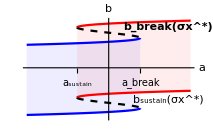
-Graphics-(a) coupling = σ x with σ < 0

```mathematica
panel1=Module[{masterFlow,slaveFlow,slaveSlaveFlow,coupling,a0=-1,x0=-.6,y0=-.6,z0=-.6,yFixedPoints,zFixedPoints,sep="\t",masterSNBs,slaveSNBs,ϵ0=-.1,b0=-1,c0=-1,fs=13,fsTicks=11,imgSize=imageSizeForFiguresWithVariousCouplings,aspectRatio=1/GoldenRatio,upperColor=Red,lowerColor=Blue,pointSize=.035,font="Times"},
Block[{a,b,x},
masterFlow=-x^3+x+a;
coupling=#1 #2&;
slaveFlow=-y^3+y+b+coupling[x,ϵ];
slaveSlaveFlow=-z^3+z+c+coupling[y,ϵ];

x0=First[Sort[Select[x/.Solve[(masterFlow/.a->a0)==0,x],Im[#]==0&],Abs[#1-x0]<Abs[#2-x0]&]];
y0=First[Sort[Select[y/.Solve[(slaveFlow/.{b->b0,x->x0,ϵ->ϵ0})==0,y],Im[#]==0.&],Abs[#1-y0]<Abs[#2-y0]&]];
masterSNBs=Evaluate[a/.Solve[{masterFlow==0,D[masterFlow,x]==0},{x,a}]];
slaveSNBs=Evaluate[b/.NSolve[({slaveFlow==0,D[slaveFlow,y]==0}/.{x->x0,ϵ->ϵ0}),{y,b}]];

yFixedPoints=y/.Quiet[Solve[(slaveFlow/.{x->x0,ϵ->ϵ0})==0,y]];
zFixedPoints=z/.Quiet[Solve[(slaveSlaveFlow/.{y->y0,ϵ->ϵ0})==0,z]];

Labeled[Plot[Evaluate@Flatten[computeSNBsForB[a,ϵ0,coupling]/.Solve[masterFlow==0,x]],{a,-1,1},AxesLabel->(Style[#,{FontSize->fs,Italic,FontFamily->font}]&/@{"a","b"(*Row[{"b_sustain(x^*),",Style[" b_break(x^*)",Bold]}]*)}),PlotStyle->{{Blue},{Blue,Thick},{Red},{Red,Thick},{Black,Dashed},{Black,Dashed,Thick}},Filling->{1->{{2},Directive[Lighter@Blue,Opacity[.1]]},3->{{4},Directive[Lighter@Red,Opacity[.1]]}},ImageSize->imgSize,PlotRange->plotRangeForFiguresWithVariousCouplings(*{-.5,.5}*),Ticks->{{{-2/(3 √3),Style["a_sustain",{FontFamily->font,FontSize->fs}]},{2/(3 √3),Style["a_break",{FontFamily->font,FontSize->fs}]}},None},Epilog->{{PointSize[Large],If[x0≤-1/(√3),Blue,Red],Point[{a0,b0}]}}~Join~{Inset[Style["b_break(σx^*)",{FontSize->fsTicks,FontFamily->font,Bold}],Scaled[{.85,.92}]],Inset[Style["b_sustain(σx^*)",{FontFamily->font,FontSize->fsTicks}],Scaled[{.85,.2}]](*,Inset[Style["B",FontSize->fs],Scaled[{.05,.8}]]*)}],
Style["(a) coupling = σ x with σ < 0",{FontSize->fs,FontFamily->font}],Bottom]

]]
```

#### panel (b)

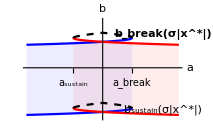
-Graphics-(b) coupling = σ |x| with σ > 0

```mathematica
panel2=Module[{masterFlow,slaveFlow,slaveSlaveFlow,coupling,a0=-1,x0=-.6,y0=-.6,z0=-.6,yFixedPoints,zFixedPoints,sep="\t",masterSNBs,slaveSNBs,slaveSNBfunction,ϵ0=.1,b0=-1,c0=-1,fs=13,fsTicks=11,imgSize=imageSizeForFiguresWithVariousCouplings,aspectRatio=1/GoldenRatio,upperColor=Red,lowerColor=Blue,pointSize=.035,font="Times"},
Block[{a,b,x},
masterFlow=-x^3+x+a;
coupling=Abs[#1] #2&;
slaveFlow=-y^3+y+b+coupling[x,ϵ];
slaveSlaveFlow=-z^3+z+c+coupling[y,ϵ];

x0=First[Sort[Select[x/.Solve[(masterFlow/.a->a0)==0,x],Im[#]==0&],Abs[#1-x0]<Abs[#2-x0]&]];
y0=First[Sort[Select[y/.Solve[(slaveFlow/.{b->b0,x->x0,ϵ->ϵ0})==0,y],Im[#]==0.&],Abs[#1-y0]<Abs[#2-y0]&]];
masterSNBs=Evaluate[a/.Solve[{masterFlow==0,D[masterFlow,x]==0},{x,a}]];
slaveSNBs=Evaluate[b/.NSolve[({slaveFlow==0,D[slaveFlow,y]==0}/.{x->x0,ϵ->ϵ0}),{y,b}]];

yFixedPoints=y/.Quiet[Solve[(slaveFlow/.{x->x0,ϵ->ϵ0})==0,y]];

slaveSNBfunction=(Function[x,If[Abs[Im[x]]<10^-6.,-2/(3 √3)-ϵ0 Abs[x]]]/@{-(2/3)^(1/3)/((-9 a+√3 √(-4+27 a^2))^(1/3))-((-9 a+√3 √(-4+27 a^2))^(1/3))/(2^(1/3) 3^(2/3)),(1+ⅈ √3)/(2^(2/3) 3^(1/3) (-9 a+√3 √(-4+27 a^2))^(1/3))+((1-ⅈ √3) (-9 a+√3 √(-4+27 a^2))^(1/3))/(2 2^(1/3) 3^(2/3)),(1-ⅈ √3)/(2^(2/3) 3^(1/3) (-9 a+√3 √(-4+27 a^2))^(1/3))+((1+ⅈ √3) (-9 a+√3 √(-4+27 a^2))^(1/3))/(2 2^(1/3) 3^(2/3))})~Join~(Function[x,If[Abs[Im[x]]<10^-6.,2/(3 √3)-ϵ0 Abs[x]]]/@{-(2/3)^(1/3)/((-9 a+√3 √(-4+27 a^2))^(1/3))-((-9 a+√3 √(-4+27 a^2))^(1/3))/(2^(1/3) 3^(2/3)),(1+ⅈ √3)/(2^(2/3) 3^(1/3) (-9 a+√3 √(-4+27 a^2))^(1/3))+((1-ⅈ √3) (-9 a+√3 √(-4+27 a^2))^(1/3))/(2 2^(1/3) 3^(2/3)),(1-ⅈ √3)/(2^(2/3) 3^(1/3) (-9 a+√3 √(-4+27 a^2))^(1/3))+((1+ⅈ √3) (-9 a+√3 √(-4+27 a^2))^(1/3))/(2 2^(1/3) 3^(2/3))});


Labeled[Plot[
slaveSNBfunction,{a,-1,1},AxesLabel->(Style[#,{FontSize->fs,Italic,FontFamily->font}]&/@{"a","b"}),PlotStyle->{{lowerColor},{upperColor},{Black,Dashed},{lowerColor,Thick},{upperColor,Thick},{Black,Dashed,Thick}},Filling->{1->{{4},{Directive[Lighter@lowerColor,Opacity[.1]]}},2->{{5},Directive[Lighter@upperColor,Opacity[.1]]}},ImageSize->imgSize,PlotRangeClipping->False,PlotRange->plotRangeForFiguresWithVariousCouplings(*{-.7,.5}*)(*{-.5,.5}*),Ticks->{{{-2/(3 √3),Style["a_sustain",{FontFamily->font,FontSize->fsTicks}]},{2/(3 √3),Style["a_break",FontFamily->font,FontSize->fsTicks]}},None},Epilog->{Inset[Style["b_break(σ|x^*|)",{FontFamily->font,FontSize->fsTicks,Bold}],Scaled[{.88,.84}]],Inset[Style["b_sustain(σ|x^*|)",{FontFamily->font,FontSize->fsTicks}],Scaled[{.88,.10}]]}]
,Style["(b) coupling = σ |x| with σ > 0",{FontSize->fs,FontFamily->font}],Bottom]

]]
```

#### panel (c)

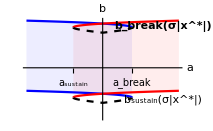
-Graphics-(c) coupling = σ |x| with σ < 0

```mathematica
panel3=Module[{masterFlow,slaveFlow,slaveSlaveFlow,coupling,a0=-1,x0=-.6,y0=-.6,z0=-.6,yFixedPoints,zFixedPoints,sep="\t",masterSNBs,slaveSNBs,slaveSNBfunction,ϵ0=-.1,b0=-1,c0=-1,fs=13,fsTicks=11,imgSize=imageSizeForFiguresWithVariousCouplings,aspectRatio=1/GoldenRatio,upperColor=Red,lowerColor=Blue,pointSize=.035,font="Times"},
Block[{a,b,x},
masterFlow=-x^3+x+a;
coupling=Abs[#1] #2&;
slaveFlow=-y^3+y+b+coupling[x,ϵ];
slaveSlaveFlow=-z^3+z+c+coupling[y,ϵ];

x0=First[Sort[Select[x/.Solve[(masterFlow/.a->a0)==0,x],Im[#]==0&],Abs[#1-x0]<Abs[#2-x0]&]];
y0=First[Sort[Select[y/.Solve[(slaveFlow/.{b->b0,x->x0,ϵ->ϵ0})==0,y],Im[#]==0.&],Abs[#1-y0]<Abs[#2-y0]&]];
masterSNBs=Evaluate[a/.Solve[{masterFlow==0,D[masterFlow,x]==0},{x,a}]];
slaveSNBs=Evaluate[b/.NSolve[({slaveFlow==0,D[slaveFlow,y]==0}/.{x->x0,ϵ->ϵ0}),{y,b}]];
(*Print[slaveSNBs];*)

yFixedPoints=y/.Quiet[Solve[(slaveFlow/.{x->x0,ϵ->ϵ0})==0,y]];

slaveSNBfunction=
Evaluate@(Function[x,If[Abs[Im[x]]<10^-6.,-2/(3 √3)-ϵ0 Abs[x](*{-2/(3 √3)-ϵ0 Abs[x],2/(3 √3)-ϵ0 Abs[x]}*)]]/@{-(2/3)^(1/3)/((-9 a+√3 √(-4+27 a^2))^(1/3))-((-9 a+√3 √(-4+27 a^2))^(1/3))/(2^(1/3) 3^(2/3)),(1+ⅈ √3)/(2^(2/3) 3^(1/3) (-9 a+√3 √(-4+27 a^2))^(1/3))+((1-ⅈ √3) (-9 a+√3 √(-4+27 a^2))^(1/3))/(2 2^(1/3) 3^(2/3)),(1-ⅈ √3)/(2^(2/3) 3^(1/3) (-9 a+√3 √(-4+27 a^2))^(1/3))+((1+ⅈ √3) (-9 a+√3 √(-4+27 a^2))^(1/3))/(2 2^(1/3) 3^(2/3))})~Join~(Function[x,If[Abs[Im[x]]<10^-6.,2/(3 √3)-ϵ0 Abs[x]]]/@{-(2/3)^(1/3)/((-9 a+√3 √(-4+27 a^2))^(1/3))-((-9 a+√3 √(-4+27 a^2))^(1/3))/(2^(1/3) 3^(2/3)),(1+ⅈ √3)/(2^(2/3) 3^(1/3) (-9 a+√3 √(-4+27 a^2))^(1/3))+((1-ⅈ √3) (-9 a+√3 √(-4+27 a^2))^(1/3))/(2 2^(1/3) 3^(2/3)),(1-ⅈ √3)/(2^(2/3) 3^(1/3) (-9 a+√3 √(-4+27 a^2))^(1/3))+((1+ⅈ √3) (-9 a+√3 √(-4+27 a^2))^(1/3))/(2 2^(1/3) 3^(2/3))});


Labeled[Plot[
slaveSNBfunction,{a,-1,1},AxesLabel->(Style[#,{FontSize->fs,Italic,FontFamily->font}]&/@{"a","b"}),PlotStyle->{{lowerColor},{upperColor},{Black,Dashed},{lowerColor,Thick},{upperColor,Thick},{Black,Dashed,Thick}},Filling->{1->{{4},{Directive[Lighter@lowerColor,Opacity[.1]]}},2->{{5},Directive[Lighter@upperColor,Opacity[.1]]}},ImageSize->imgSize,PlotRangeClipping->False,PlotRange->plotRangeForFiguresWithVariousCouplings(*{-.7,.5}*)(*{-.5,.5}*),Ticks->{{{-2/(3 √3),Style["a_sustain",{FontFamily->font,FontSize->fsTicks}]},{2/(3 √3),Style["a_break",{FontSize->fsTicks,FontFamily->font}]}},None},Epilog->{Inset[Style["b_break(σ|x^*|)",{FontSize->fsTicks,FontFamily->font,Bold}],Scaled[{.88,.92}]],Inset[Style["b_sustain(σ|x^*|)",{FontFamily->font,FontSize->fsTicks}],Scaled[{.88,.2}]]}]
,Style["(c) coupling = σ |x| with σ < 0",{FontSize->fs,FontFamily->font}],Bottom]

]]
```

### Create the figure by combining the three panels

```mathematica
Row[{panel1,panel2,panel3},"  "]
```

-Graphics-(a) coupling = σ x with σ < 0-Graphics-(b) coupling = σ |x| with σ > 0-Graphics-(c) coupling = σ |x| with σ < 0

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"figureS2.pdf"}],%]
```

## Figure 3: x drives y drives z

### Derivation

First, let’s clear the variables x and a:

```mathematica
ClearAll[x,a]
```

The saddle-node bifurcations for the master system are a_break=2/(3 √3),a_sustain =-2/(3 √3):

```mathematica
Solve[{-x^3+x+a==0,D[-x^3+x+a,x]==0},{x,a}]
```

{{x→-1/(√3),a→2/(3 √3)},{x→1/(√3),a→-2/(3 √3)}}

At a_break=2/(3 √3), x^* jumps from -1/(√3) to 2/(√3):

```mathematica
Solve[-x^3+x+a==0/.a->2/(3 √3)]
```

{{x→-1/(√3)},{x→-1/(√3)},{x→2/(√3)}}

At a_sustain=-2/(3 √3), x^* jumps from 1/(√3) to -2/(√3):

```mathematica
Solve[-x^3+x+a==0/.a->-2/(3 √3)]
```

{{x→-2/(√3)},{x→1/(√3)},{x→1/(√3)}}

When a=a_break and x^* is on the upper branch (x^*=2/(√3)), y_break(a_break)=-(2 (1+3 ϵ))/(3 √3) and y_sustain(a_break)=(2 (1-3 ϵ))/(3 √3).

```mathematica
Simplify@Solve[{-y^3+y+b+x ϵ==0,D[-y^3+y+b+x ϵ,y]==0}/.{x->2/(√3)},{y,b}]
```

{{y→-1/(√3),b→(2 (1-3 ϵ))/(3 √3)},{y→1/(√3),b→-(2 (1+3 ϵ))/(3 √3)}}

When a=a_break and x^* is on the lower branch (x^*=-1/(√3)), y_break(a_break)=(2+3 ϵ)/(3 √3) and y_sustain(a_break)=(-2+3 ϵ)/(3 √3).

```mathematica
Simplify@Solve[{-y^3+y+b+x ϵ==0,D[-y^3+y+b+x ϵ,y]==0}/.{x->-1/(√3)},{y,b}]
```

{{y→-1/(√3),b→(2+3 ϵ)/(3 √3)},{y→1/(√3),b→(-2+3 ϵ)/(3 √3)}}

In general, the values of b_break and b_sustain is 2/(3 √3)-x ϵ and -2/(3 √3)-x ϵ

```mathematica
Simplify@Solve[{-y^3+y+b+x ϵ==0,D[-y^3+y+b+x ϵ,y]==0},{y,b}]
```

{{y→-1/(√3),b→2/(3 √3)-x ϵ},{y→1/(√3),b→-2/(3 √3)-x ϵ}}

### Create Figure 3

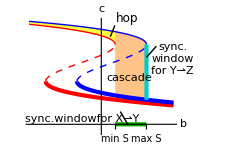

```mathematica
Module[{masterFlow,slaveFlow,slaveSlaveFlow,coupling,a0=-1,x0=-.6,y0=-.6,z0=-.6,yFixedPoints,zFixedPoints,sep="\t",
fs=12,fsTicks=11,imgSize=(*1.5  8.7 72/2.54*)1. 8.4/2.54*72,aspectRatio=1/GoldenRatio,upperColor=Red,lowerColor=Blue,
ϵ0=.2,b0=-.5,c0=-.5,font="Times"},
Block[{a,b,x},
masterFlow=-x^3+x+a;
coupling=#1 #2&;
slaveFlow=-y^3+y+b+coupling[x,ϵ];
slaveSlaveFlow=-z^3+z+c+coupling[y,ϵ];

x0=First[Sort[Select[x/.Solve[(masterFlow/.a->a0)==0,x],Im[#]==0&],Abs[#1-x0]<Abs[#2-x0]&]];
y0=First[Sort[Select[y/.Solve[(slaveFlow/.{b->b0,x->x0,ϵ->ϵ0})==0,y],Im[#]==0.&],Abs[#1-y0]<Abs[#2-y0]&]];
z0=First[Sort[Select[z/.Solve[(slaveSlaveFlow/.{(*b->b0,x->x0,*)ϵ->ϵ0,y->y0,c->c0})==0,z],Im[#]==0.&],Abs[#1-z0]<Abs[#2-z0]&]];

Quiet[
Show[
Plot[{{2/(3 √3)-coupling[y,ϵ],-2/(3 √3)-coupling[y,ϵ]}/.Part[NSolve[slaveFlow==0,y],1](*/.Solve[masterFlow==0,x]*)/.{ϵ->ϵ0,a->2/(3 √3),x->2/(√3)}
,
{2/(3 √3)-coupling[y,ϵ],-2/(3 √3)-coupling[y,ϵ]}/.Part[NSolve[slaveFlow==0,y],1]/.{ϵ->ϵ0,a->2/(3 √3),x->-1/(√3)}
},{b,-.8(*(-2+3 ϵ0)/(3 √3)*),(2 (1-3 ϵ0))/(3 √3)},PlotStyle->None,Filling->{1->{{2},Directive[Yellow,Opacity[.5]]}}],
Plot[{{2/(3 √3)-coupling[y,ϵ],-2/(3 √3)-coupling[y,ϵ]}/.Part[#,2]&@Solve[slaveFlow==0,y](*/.Solve[masterFlow==0,x]*)/.{ϵ->ϵ0,a->2/(3 √3),x->2/(√3)},
{2/(3 √3)-coupling[y,ϵ],-2/(3 √3)-coupling[y,ϵ]}/.Part[NSolve[slaveFlow==0,y],-3](*/.Solve[masterFlow==0,x]*)/.{ϵ->ϵ0,a->2/(3 √3),x->-1/(√3)}
},{b,(2 (1-3 ϵ0))/(3 √3),(2+3 ϵ0)/(3 √3)-.002},PlotStyle->None,Filling->{1->{{2},Directive[Lighter@Orange,Opacity[.45]]}}],

Plot[Evaluate[Flatten[

(*{Subscript[c, break],Subscript[c, sustain]} for x^* on its upper branch at Subscript[a, break]*)
{2/(3 √3)-coupling[y,ϵ],-2/(3 √3)-coupling[y,ϵ]}/.Solve[slaveFlow==0,y]/.{ϵ->ϵ0,a->2/(3 √3),x->2/(√3)}
]~Join~Flatten[

(*{Subscript[c, break],Subscript[c, sustain]} for x^* on its lower branch*)
{2/(3 √3)-coupling[y,ϵ],-2/(3 √3)-coupling[y,ϵ]}/.Solve[slaveFlow==0,y]/.{ϵ->ϵ0,a->2/(3 √3),x->-1/(√3)}
]],{b,-.8,.8},
PlotStyle->{{Red,AbsoluteThickness[1]},None,{Red,AbsoluteThickness[3]},None,{Red,Dashed,AbsoluteThickness[1]},None,{Blue,AbsoluteThickness[1]},Blue,{Blue,AbsoluteThickness[3]},None,{Dashed,Blue,AbsoluteThickness[1]},{Dashed,Black}},
PlotLegends->Placed[LineLegend[{Directive[lowerColor],Directive[upperColor],{Gray,AbsoluteThickness[3]},Directive@@{Dashed,Gray,AbsoluteThickness[1]},{Gray,AbsoluteThickness[1]}},(Style[#,{FontSize->fsTicks,FontFamily->font}]&/@{"lower ",(*"middle ",*)"upper branch","lower","middle","upper branch"}),LegendLayout->(Column[{Row[{Style["SuperscriptBox[
 StyleBox[\"x\",\nFontSlant->\"Italic\"], \"*\"] on its ",{FontSize->fsTicks,FontFamily->font}],Style["lower",{FontSize->fsTicks,FontFamily->font,lowerColor}],Style[", ",{FontSize->fsTicks,FontFamily->font}],Style["upper ",{FontSize->fsTicks,FontFamily->font,upperColor}],Style["branch",{FontSize->fsTicks,FontFamily->font}]}],Row[{Style["SuperscriptBox[
 StyleBox[\"y\",\nFontSlant->\"Italic\"], \"*\"] on its ",{FontSize->fsTicks,FontFamily->font}]}~Join~(Row[#," "]&/@Take[#,-3])," "]},Left,0]&),LegendMarkerSize->12],Below]
]
,AxesLabel->(Style[#,{FontSize->fs,FontFamily->font}]&/@{"b",(*"c"*)"c"}),PlotRange->{-.05(*-.7*),.65},Ticks->{{{(2 (1-3 ϵ0))/(3 √3),Style["min S",{FontFamily->font,FontSize->fsTicks}]},{-(2 (1+3 ϵ0))/(3 √3),Style["-max S",{FontFamily->font,FontSize->fsTicks}]},{(2+3 ϵ0)/(3 √3),Style["max S",{FontFamily->font,FontSize->fsTicks}]},{(-2+3 ϵ0)/(3 √3),Style["-min S",{FontFamily->font,FontSize->fsTicks}]}},None},AxesOrigin->{0,0},AspectRatio->aspectRatio,AspectRatio->aspectRatio,ImageSize->imgSize,Epilog->{{Darker@Green,AbsoluteThickness[3],Line[{{(2 (1-3 ϵ0))/(3 √3),0},{(2+3 ϵ0)/(3 √3),0}}]},
{Darker[#,.2]&@Cyan,AbsoluteThickness[3],Line[{{(2+3 ϵ0)/(3 √3),(2/(3 √3)-coupling[y,ϵ]/.Part[#,2]&@NSolve[slaveFlow==0,y]/.{ϵ->ϵ0,a->2/(3 √3),x->-1/(√3)})/.b->(2+3 ϵ0)/(3 √3)},
{(2+3 ϵ0)/(3 √3),(2/(3 √3)-coupling[y,ϵ]/.Part[#,1]&@NSolve[slaveFlow==0,y]/.{ϵ->ϵ0,a->2/(3 √3),x->-1/(√3)})/.b->(2+3 ϵ0)/(3 √3)}}]},
{Line[{{0.1,.55},{.15,.62}}]},
Inset[Style["hop",{FontFamily->font,FontSize->fs}],{.13+.03,.622},{-.9,-.6}],
Inset[Column[{Style["cascade",{FontFamily->font,FontSize->fs}]},Alignment->Center,Spacings->{0,.1}],{(*.29*).31,.29}],
{Line[{{(2+3 ϵ0)/(3 √3),.39+.03},{.58+.03,.46+.03}}]},
Inset[Column[{Style["sync.",{FontFamily->font,FontSize->fs}],Style["window",{FontFamily->font,FontSize->fs}],Style["for Y⇀Z",{FontFamily->font,FontSize->fs}]},Alignment->Left,Spacings->{0,.1}],{.79,.41}],
BezierCurve[{{{(2+3 ϵ0)/(3 √3),(2 (1-3 ϵ0))/(3 √3)}.{.4,.6},0},{.21,.08}}],
Inset[Row[{Style["sync.",{FontFamily->font,FontSize->fs}],Style["window",{FontFamily->font,FontSize->fs}],Style["for X⇀Y",{FontFamily->font,FontSize->fs}]}," ",Alignment->Center(*,Spacings->{0,.1}*)],{-.21,0},{0,-2.1}](*,
Inset[Style["c_break(y^*)",{FontFamily->font,FontSize->fs}],{-.1,.5}]*)
},PlotRangeClipping->False]
,Solve::ratnz]

]
]
```

#### export Figure 3

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"figure3.pdf"}],%];
```